# Auxiliary Functions

```mathematica
Quiet@Remove["Global`*"]
FormattingStrings[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\right)"->"\\right)"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"phiNF"->"{phiNF}"];
auxiliarystring=StringReplace[auxiliarystring,"psiNF"->"{psiNF}"];
auxiliarystring=ToExpression[auxiliarystring,TeXForm];
Return[auxiliarystring]
]
FormattingStringsCommaSplit[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\right)"->"\\right)"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"phiNF"->"{phiNF}"];
auxiliarystring=StringReplace[auxiliarystring,"psiNF"->"{psiNF}"];
auxiliarystring=StringSplit[auxiliarystring,","];
Return[auxiliarystring]
]
```

## Vector field and equilibrium point

```mathematica
SetDirectory[NotebookDirectory[]];
null[_String]:=Null;
eqbool=1;
If[FileExistsQ["Fixed parameter values.txt"],
Nparametereval=Length@ReadList["Fixed parameter values.txt",null@String,NullRecords->True];
,
Print["The file 'Fixed parameter values.txt' could not be found. Run the Python script first."];
Quit[];
]
If[Nparametereval>0,
For[parnum=1,parnum<=Nparametereval,parnum++,
aux=ReadLine["Fixed parameter values.txt"];
aux=FormattingStringsCommaSplit[aux];
parname=ToExpression[aux[[1]],TeXForm];
parval=ToExpression[aux[[2]],TeXForm];
parname//Evaluate=parval;
];
Close["Fixed parameter values.txt"];
]
ii[n_,x_]=√(π/(2x))*BesselI[n+1/2,x];
If[FileExistsQ["Kinetics.txt"],
nvar=Length@ReadList["Kinetics.txt",null@String,NullRecords->True];
,
Print["The file 'Kinetics.txt' could not found. Run the Python script first."];
Quit[];
]
nvar=nvar/2;
kinetics=Range[2*nvar];
var=Range[2*nvar];
For[varnum=1,varnum<=2*nvar,varnum++,
kinetics[[varnum]]=ReadLine["Kinetics.txt"];
kinetics[[varnum]]=FormattingStrings[kinetics[[varnum]]];
If[FileExistsQ["List of variables.txt"],
var[[varnum]]=ReadLine["List of variables.txt"];
,
Print["The file 'List of variables.txt' could not be found. Run the Python script first."];
Quit[]
];
var[[varnum]]=ToExpression[var[[varnum]],TeXForm];
];
Close["Kinetics.txt"];
Close["List of variables.txt"];
Bmatrix=-D[kinetics[[1;;nvar]],{var[[1;;nvar]]}];
Kmatrix=D[kinetics[[nvar+1;;2*nvar]],{var[[1;;nvar]]}];
Diffusionmatrix=Import["Diffusion matrix for Mathematica.json"];
Diffusionmatrix=ToExpression[Diffusionmatrix,TeXForm];
Diffbulk=Diffusionmatrix[[1;;nvar,1;;nvar]];
omega=DiagonalMatrix[Table[√((Bmatrix[[varnum]][[varnum]])/Diffbulk[[varnum,varnum]]),{varnum,nvar}]];
i0omegaR=DiagonalMatrix[Table[ii[0,omega[[varnum,varnum]]*R],{varnum,nvar}]];
i0primeomegaR=DiagonalMatrix[Table[D[ii[0,x],x]/.x->omega[[varnum,varnum]]*R,{varnum,nvar}]];
ilomegaR=DiagonalMatrix[Table[ii[l,omega[[varnum,varnum]]*R],{varnum,nvar}]];
ilprimeomegaR=DiagonalMatrix[Table[D[ii[l,x],x]/.x->omega[[varnum,varnum]]*R,{varnum,nvar}]];
S0=Dot[Inverse[Dot[Diffbulk,i0primeomegaR,omega]+Dot[Kmatrix,i0omegaR]],Kmatrix];
Sl=Dot[Inverse[Dot[Diffbulk,ilprimeomegaR,omega]+Dot[Kmatrix,ilomegaR]],Kmatrix];
If[eqbool==1,
eqs=Solve[kinetics[[nvar+1;;2*nvar]]==0/.Table[var[[varnum]]->i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}],var[[nvar+1;;2*nvar]]];
If[Length[eqs]>1,
eqnumber=3;
If[eqnumber==0,
eq={0};
,
eq=eqs[[eqnumber]]//Simplify;]
,
eqnumber=1];
eq=eqs[[eqnumber]];
,
eq={0};
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

# Fixed parameters and Turing bifurcation variables

```mathematica
SetDirectory[NotebookDirectory[]];
lvalues={};
If[FileExistsQ["Values of l.txt"],
numberofl=Length@ReadList["Values of l.txt",null@String,NullRecords->True];
,
Print["The file 'Values of l.txt' could not be found. Run the Python script first."];
Quit[]
];
For[lnum=1,lnum<=numberofl,lnum++,
aux=ReadLine["Values of l.txt"];
AppendTo[lvalues,ToExpression[aux]];
];
zerodet=Range[numberofl];
For[counter=1,counter<=numberofl,counter++,
If[FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "/Determinant l=" <> ToString[lvalues[[counter]]] <> ".txt"],
zerodet[[counter]]=Import["l=" <> ToString[lvalues[[counter]]]<>"/Determinant l=" <> ToString[lvalues[[counter]]] <> ".txt"];
zerodet[[counter]]=FormattingStrings[zerodet[[counter]]];
,
Print["The file 'l= " <> ToString[lvalues[[counter]]]<>"/Determinant l= <> ToString[lvalues[[counter]]] <> .txt' could not be found. Run the Python script first."];
Quit[];
]
]
```

# Parameters on the axes of the bifurcation diagram

```mathematica
npar=2;
par=Range[npar];
lowerbound=Range[npar];
upperbound=Range[npar];
For[parnum=1,parnum<=npar,parnum++,
If[FileExistsQ["Parameters on axes.txt"],
aux=ReadLine["Parameters on axes.txt"];
,
Print["The file 'Parameters on axes.txt' could not be found. Run the Python script first."];
Quit[]
];
aux=FormattingStringsCommaSplit[aux];
par[[parnum]]=ToExpression[aux[[1]],TeXForm];
lowerbound[[parnum]]=ToExpression[aux[[2]],TeXForm];
upperbound[[parnum]]=ToExpression[aux[[3]],TeXForm];
]
Close["Parameters on axes.txt"];
If[FileExistsQ["Actual names of parameters.txt"],
aux=ReadLine["Actual names of parameters.txt"];
aux=FormattingStringsCommaSplit[aux];
newparam1=ToExpression[aux[[1]],TeXForm];
newparam2=ToExpression[aux[[2]],TeXForm];
Close["Actual names of parameters.txt"];
,
newparam1=par[[1]];
newparam2=par[[2]];
]
```

# Bifurcation curves

```mathematica
initialt=-1000;
finalt=1000;
curvespeed=10^-2;
tol=10^-10;
simpleeq=0;
smalldifferential=0.001;
variabledependence=Table[var[[varnum]]->var[[varnum]][time],{varnum,2*nvar}];
kineticsaux=Table[var[[varnum]]-i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}]/.variabledependence/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time];
kineticsaux=Join[kineticsaux,kinetics[[nvar+1;;2*nvar]]/.variabledependence/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]];
solutioncurves=Range[Length[zerodet]];
allvar=Table[var[[varnum]],{varnum,2*nvar}];
AppendTo[allvar,par[[1]]];
AppendTo[allvar,par[[2]]];
allvartimedependent=Table[allvar[[varnum]][time],{varnum,Length[allvar]}];
For[counter=1,counter<=Length[zerodet],counter++,
zerodetaux=zerodet[[counter]]/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence;
equations=Append[kineticsaux,zerodetaux];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+∑_(varnum=1)^(2*nvar) (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
If[FileExistsQ["Initial conditions for Turing bifurcation curves.txt"],
numberofbifurcationcurves=Length@ReadList["Initial conditions for Turing bifurcation curves.txt",null@String,NullRecords->True];
,
Print["The file 'Initial conditions for Turing bifurcation curves.txt' could not be found. Run the Python script first."];
Quit[];
];
initialvalueTuring={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
aux=ReadLine["Initial conditions for Turing bifurcation curves.txt"];
aux=FormattingStringsCommaSplit[aux];
AppendTo[initialvalueTuring,{ToExpression[aux[[1]],TeXForm],ToExpression[aux[[2]],TeXForm]}];
];
Close["Initial conditions for Turing bifurcation curves.txt"];
solutioncurves[[counter]]={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
fixedparameter=Position[par,initialvalueTuring[[bifnum]][[1]]][[1]][[1]];
If[fixedparameter==1,
anotherparameter=2;
,
anotherparameter=1;
];
If[simpleeq==1 && Length[eq]>1,initialvalues=Quiet@Chop[NSolve[zerodet[[counter]]==0/.eq/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],{par[[anotherparameter]]}//Evaluate],tol];
,
initialvalues=Quiet@Chop[NSolve[Join[{zerodet[[counter]]},kinetics[[nvar+1;;2*nvar]]/.Table[var[[varnum]]->i0omegaR[[varnum,varnum]]*S0[[varnum,varnum]]*var[[varnum+nvar]],{varnum,nvar}]]==0/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]],Join[{par[[anotherparameter]]},var[[nvar+1;;2*nvar]]]//Evaluate],tol];
];
initialvalues=Table[Table[initialvalues[[initialsolnum]][[varnum]][[1]]->Re[initialvalues[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvalues[[initialsolnum]]]}],{initialsolnum,Length[initialvalues]}];
initialvalues=DeleteDuplicates[initialvalues];
For[initialsolnum=1,initialsolnum<=Length[initialvalues],initialsolnum++,
If[simpleeq==1 && Length[eq]>1,
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]];
initialvalues[[initialsolnum]]=Join[initialvalues[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.initialvalues[[initialsolnum]]),{varnum,2*nvar}]],
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]]
];
If[(Abs[zerodet[[counter]]]<tol/.initialvalues[[initialsolnum]]) && (par[[anotherparameter]]/.initialvalues[[initialsolnum]])∈Reals && If[Length[eq]>1,Norm[(var/.eq)-var/.initialvalues[[initialsolnum]]]<tol, True] && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]/.initialvalues[[initialsolnum]],
dereval=Table[par[[parnum]][0]->(par[[parnum]]/.par[[fixedparameter]]->initialvalueTuring[[bifnum]][[2]]/.initialvalues[[initialsolnum]]),{parnum,npar}];
dereval=Join[dereval,Table[var[[varnum]][0]->(var[[varnum]]/.initialvalues[[initialsolnum]]),{varnum,2*nvar}]];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Append[equations,par[[fixedparameter]][0]==initialvalueTuring[[bifnum]][[2]]];
AppendTo[equationsaux,par[[anotherparameter]][0]==(par[[anotherparameter]]/.initialvalues[[initialsolnum]])];
equationsaux=Join[equationsaux,Table[var[[varnum]][0]==(var[[varnum]]/.initialvalues[[initialsolnum]]),{varnum,nvar+1,2*nvar}]];
equationsaux=Join[equationsaux,Table[var[[varnum]]'[0]==(var[[varnum]]'[0]/.initialderivatives[[dernumber]]),{varnum,nvar+1,2*nvar}]];
equationsaux=Join[equationsaux,Table[par[[parnum]]'[0]==(par[[parnum]]'[0]/.initialderivatives[[dernumber]]),{parnum,npar}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]<=lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]>=upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]<=lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]>=upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[Length[sol]>0&& sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves[[counter]],sol];
]
]
]
]
]
]
If[Length[solutioncurves]==0,Print["This script could not find a Turing bifurcation curve nor a BD-line for your desired parameters. Try changing the integration method."]]
```

# Bifurcation diagram plotting

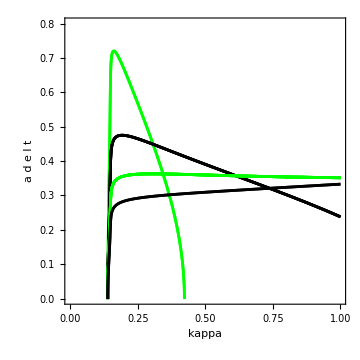

```mathematica
If[ValueQ[critchange] && Length[critchange]>=1,
critpoints=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange[[critnum]][[2]]]}],{critnum,Length[critchange]}];
]
bifcurveplot=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
bifcurveplot[[counter]]={};
For[outersolnum=1,outersolnum<=Length[solutioncurves[[counter]]],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[counter]][[outersolnum]]],innersolnum++,
If[OddQ[lvalues[[counter]]],
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurves[[counter]][[outersolnum]][[innersolnum]],{time,solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Green,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}},PlotLabel->"l=" <> ToString[lvalues[[counter]]]];
,
tempplot=Quiet@ParametricPlot[{par[[1]][time],par[[2]][time]}/. solutioncurves[[counter]][[outersolnum]][[innersolnum]],{time,solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[counter]][[outersolnum]][[innersolnum]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotStyle->Black,PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}},PlotLabel->"l=" <> ToString[lvalues[[counter]]]];
];
AppendTo[bifcurveplot[[counter]],tempplot];
]
]
]
If[ValueQ[critpoints] && Length[critpoints]>0,
Row[(Show[#1,critpoints,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[bifcurveplot,0]];
Show[bifcurveplot,critpoints,PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
,
Row[(Show[#1,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[bifcurveplot,0]];
Show[bifcurveplot,PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
]
```

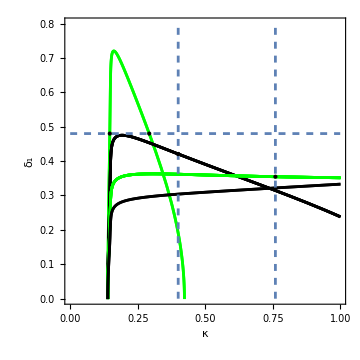

```mathematica
hl1=ParametricPlot[{t,0.48},{t,0,1},PlotStyle->Directive[Dashed]];
P1=Graphics[{PointSize[Large],Black,Point[{0.146644,0.48}]}];
P2= Graphics[{PointSize[Large],Black,Point[{0.292672,0.48}]}];
vl1=ParametricPlot[{0.4,t},{t,0,0.8},PlotStyle->Directive[Dashed]];
P3=Graphics[{PointSize[Large],Black,Point[{0.4,0.420644}]}];
vl2=ParametricPlot[{0.76,t},{t,0,0.8},PlotStyle->Directive[Dashed]];
P4=Graphics[{PointSize[Large],Black,Point[{0.76,0.354603}]}];
Show[bifcurveplot,hl1,P1,P2,vl1,P3,vl2,P3,P4,PlotLabel->"",ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]
```

# Cross-order coefficient

```mathematica
counter=4;
auxsol={{par[[1]]->0.146644,par[[2]]->0.48},
{par[[1]]->0.292672,par[[2]]->0.48},
{par[[1]]->0.4,par[[2]]->0.420644},
{par[[1]]->0.76,par[[2]]->0.354603}};
auxeq=eq/.auxsol[[counter]];
If[¬FileExistsQ["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Simple part of cross-order coefficient l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Factor to get cross-order coefficient l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> ".txt"] || ¬FileExistsQ["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Kernels.txt"],
Print["The cross-order coefficient will not be computed for l=" <> ToString[lvalues[[Max[{1,counter-1}]]]]];
,
simpleC11=Import["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Simple part of cross-order coefficient l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> ".txt"];
simpleC11=FormattingStrings[simpleC11];
factorC11=Import["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Factor to get cross-order coefficient l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> ".txt"];
factorC11=FormattingStrings[factorC11];
For[counterC11=1,counterC11<=2,counterC11++,
aux=ReadLine["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> ".txt"];
aux2=ReadLine["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Kernels.txt"];
If[counterC11==1,
crosspar=FormattingStrings[aux];
phieval=FormattingStringsCommaSplit[aux2];
,
termtodiff=FormattingStrings[aux];
psieval=FormattingStringsCommaSplit[aux2];
]
];
Close["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Term to differentiate to get cross-order coefficient l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> ".txt"];
Close["l=" <> ToString[lvalues[[Max[{1,counter-1}]]]] <> "//Kernels.txt"];
termtodiff=termtodiff/.eq;
termtodiff=D[termtodiff,crosspar];
For[varnum=0,varnum<=nvar-1,varnum++,
termtodiff=termtodiff/.Subscript[phiNF, varnum]->ToExpression[phieval[[varnum+1]],TeXForm];
termtodiff=termtodiff/.Subscript[psiNF, varnum]->ToExpression[psieval[[varnum+1]],TeXForm];
];
C11=simpleC11+factorC11*termtodiff/.auxeq/.auxsol[[counter]];
]
```

```mathematica
C11
```

112.596

```mathematica
C11
```

-6.30308

```mathematica
C11
```

-5.81929

```mathematica
C11
```

-9.44413

```mathematica
auxsol=NSolve[par[[1]][time]==0.292672/.solutioncurves[[1]][[1]][[1]],time][[1]]
par[[2]][time]/.solutioncurves[[1]][[1]][[1]]/.auxsol
auxsol2=NSolve[par[[2]][time]==0.48/.solutioncurves[[1]][[1]][[1]],time][[1]]
par[[1]][time]/.solutioncurves[[1]][[1]][[1]]/.auxsol2
C31=Import["l=1//C3 q1=0, q2=0, q3=0, m=0.txt"];
C31=FormattingStrings[C31];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C31/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence/.solutioncurves[[1]][[1]][[1]]);
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{time→-304.778}

0.48

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{time→-51.3093}

0.146644

```mathematica
toplot[time/.auxsol]
toplot[time/.auxsol2]
```

1.63523

160.42

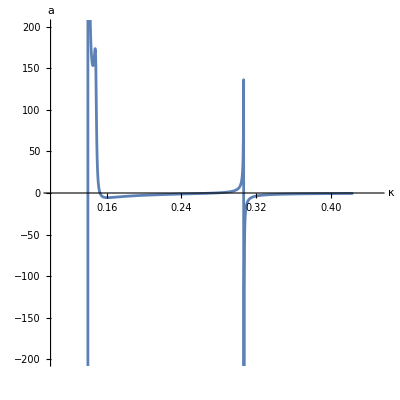

```mathematica
ParametricPlot[{par[[1]][time]/.solutioncurves[[1]][[1]][[1]],toplot[time]},{time,solutioncurves[[1]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[1]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotRange->{{0.1,0.45},{-200,200}},AspectRatio->1,AxesLabel->{"κ","a"}]
```

```mathematica
auxsol=NSolve[par[[1]][time]==0.4/.solutioncurves[[2]][[1]][[1]],time][[1]]
par[[2]][time]/.solutioncurves[[2]][[1]][[1]]/.auxsol
C22=Import["l=2//C2 q1=0, q2=0, m=0.txt"];
C22=FormattingStrings[C22];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C22/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence/.solutioncurves[[2]][[1]][[1]]);
aval=-toplot[time/.auxsol]/2
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{time→-313.317}

0.420644

0.0414126

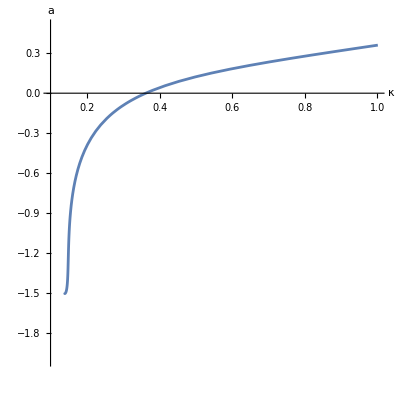

```mathematica
ParametricPlot[{par[[1]][time]/.solutioncurves[[2]][[1]][[1]],-toplot[time]/2},{time,solutioncurves[[2]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[2]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotRange->{{0.1,1.0},{-2,0.5}},AspectRatio->1,AxesLabel->{"κ","a"}]
```

```mathematica
auxsolcrit=NSolve[toplot[time]==0,time][[1]]
{par[[1]][time],par[[2]][time]}/.solutioncurves[[2]][[1]][[1]]/.auxsolcrit
C32=Import["l=2//C3 q1=0, q2=0, q3=0, m=0.txt"];
C32=FormattingStrings[C32];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C32/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence/.solutioncurves[[2]][[1]][[1]]);
bval=-toplot[time/.auxsolcrit]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{time→-303.93}

{0.362182,0.432158}

1.15796

```mathematica
auxsol=NSolve[par[[1]][time]==0.76/.solutioncurves[[3]][[1]][[1]],time][[1]]
C33=Import["l=3\\C3 q1=1, q2=1, q3=1, m=3.txt"];
C33=FormattingStrings[C33];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C33/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence/.solutioncurves[[3]][[1]][[1]]);
aval=toplot[time/.auxsol]/(2*√15)
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{time→-366.991}

-0.0252879

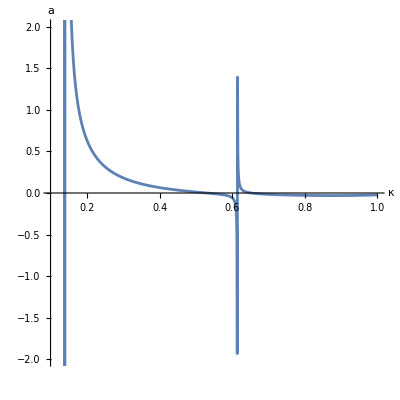

```mathematica
ParametricPlot[{par[[1]][time]/.solutioncurves[[3]][[1]][[1]],toplot[time]/(2*√15)},{time,solutioncurves[[3]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[3]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotRange->{{0.1,1.0},{-2,2}},AspectRatio->1,AxesLabel->{"κ","a"}]
```

```mathematica
C332=Import["l=3\\C3 q1=0, q2=0, q3=3, m=3.txt"];
C332=FormattingStrings[C332];
toplot=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C332/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.variabledependence/.solutioncurves[[3]][[1]][[1]]);
bval=toplot[time/.auxsol]
```

-1.03659

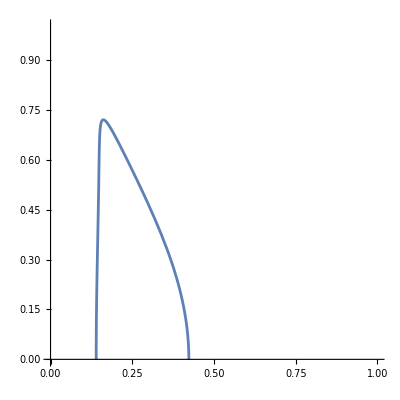

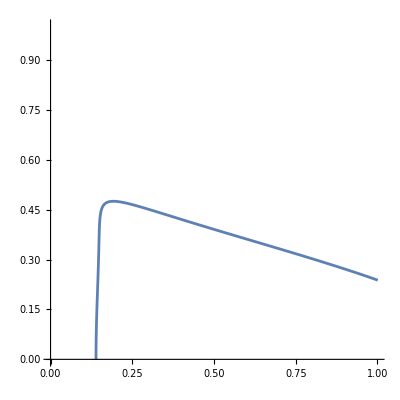

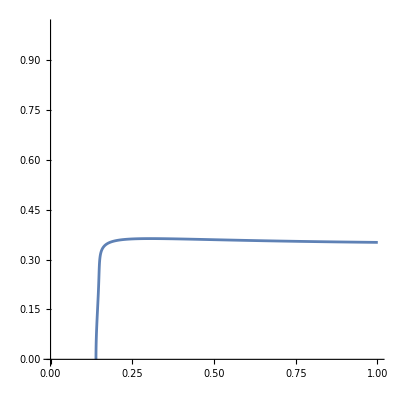

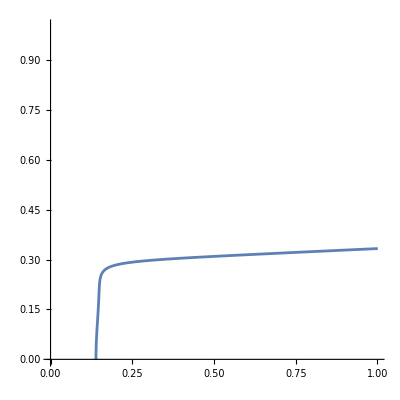

```mathematica
ParametricPlot[{ϵ[time],Subscript[δ, 1][time]}/.solutioncurves[[1]][[1]][[1]],{time,solutioncurves[[1]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[1]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotRange->{{0,1},{0,1}}]
ParametricPlot[{ϵ[time],Subscript[δ, 1][time]}/.solutioncurves[[2]][[1]][[1]],{time,solutioncurves[[2]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[2]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotRange->{{0,1},{0,1}}]
ParametricPlot[{ϵ[time],Subscript[δ, 1][time]}/.solutioncurves[[3]][[1]][[1]],{time,solutioncurves[[3]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[3]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotRange->{{0,1},{0,1}}]
ParametricPlot[{ϵ[time],Subscript[δ, 1][time]}/.solutioncurves[[4]][[1]][[1]],{time,solutioncurves[[4]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[1]],solutioncurves[[4]][[1]][[1]][[nvar+1]][[2]]["Domain"][[1]][[2]]},PlotRange->{{0,1},{0,1}}]
```

# Getting points

```mathematica
parnum=2;
(*parval=0.057;*)
parval=0.48;
fixed={par[[parnum]]->parval};
actualt=Range[Length[zerodet]];
evaluations=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
actualt[[counter]]={};
evaluations[[counter]]={};
For [outersolnum=1,outersolnum<=Length[solutioncurves[[counter]]],outersolnum++,
For [innersolnum=1,innersolnum<=Length[solutioncurves[[counter]][[outersolnum]]],innersolnum++,
tguess=Quiet@NSolve[par[[parnum]][time]-parval==0/.solutioncurves[[counter]][[outersolnum]][[innersolnum]],time];
For[solnum=1,solnum<=Length[tguess],solnum++,
If[Abs[par[[parnum]][time]-parval/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]]<tol,
AppendTo[actualt[[counter]],tguess];
AppendTo[evaluations[[counter]],Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]])},
Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[counter]][[outersolnum]][[innersolnum]]/.tguess[[solnum]]),{varnum,2*nvar}]]]
]
]
]
]
]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction::ifun will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-795.428} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
NMinimize[{Abs[par[[2]][time]-0.48]/.solutioncurves[[1]][[1]][[1]],time<-200},time][[2]]
AppendTo[evaluations[[1]],Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[1]][[1]][[1]]/.%),par[[2]]->(par[[2]][time]/.solutioncurves[[1]][[1]][[1]]/.%)},
Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[1]][[1]][[1]]/.%),{varnum,2*nvar}]]]
```

{time→-304.778}

{{ϵ→0.146644,δ_1→0.48,U→1.00448,V→0.928535,W→1.00448,Z→0.928535,u→0.177704,v→1.8466,w→0.177704,z→1.8466},{ϵ→0.146644,δ_1→0.48,U→1.00448,V→0.928535,W→1.00448,Z→0.928535,u→0.177704,v→1.8466,w→0.177704,z→1.8466},{ϵ→0.292672,δ_1→0.48,U→1.06826,V→-0.173264,W→1.06826,Z→-0.173264,u→0.815488,v→0.741357,w→0.815488,z→0.741357}}

```mathematica
evaluations[[2]]
```

{{ϵ→0.4,δ_1→0.420644,U→1.08715,V→-0.223673,W→1.08715,Z→-0.223673,u→1.00241,v→0.68968,w→1.00241,z→0.689679},{ϵ→0.4,δ_1→0.420644,U→1.08715,V→-0.223673,W→1.08715,Z→-0.223673,u→1.00241,v→0.68968,w→1.00241,z→0.689679},{ϵ→0.4,δ_1→0.420644,U→1.08715,V→-0.223673,W→1.08715,Z→-0.223673,u→1.00241,v→0.689679,w→1.00241,z→0.689679},{ϵ→0.4,δ_1→0.420644,U→1.08715,V→-0.223673,W→1.08715,Z→-0.223673,u→1.00241,v→0.689679,w→1.00241,z→0.689679}}

```mathematica
(*evaluations[[1]]*)
(*evaluations[[2]]*)
evaluations[[3]]
(*evaluations[[4]]*)
```

{{ϵ→0.76,δ_1→0.354603,U→1.12089,V→-0.190274,W→1.12089,Z→-0.190274,u→1.33956,v→0.722997,w→1.33956,z→0.722997},{ϵ→0.76,δ_1→0.354603,U→1.12089,V→-0.190274,W→1.12089,Z→-0.190274,u→1.33956,v→0.722997,w→1.33956,z→0.722997},{ϵ→0.76,δ_1→0.354603,U→1.12089,V→-0.190274,W→1.12089,Z→-0.190274,u→1.33956,v→0.722997,w→1.33956,z→0.722997},{ϵ→0.76,δ_1→0.354603,U→1.12089,V→-0.190274,W→1.12089,Z→-0.190274,u→1.33956,v→0.722997,w→1.33956,z→0.722997},{ϵ→0.76,δ_1→0.354603,U→1.12089,V→-0.190274,W→1.12089,Z→-0.190274,u→1.33956,v→0.722997,w→1.33956,z→0.722997},{ϵ→0.76,δ_1→0.354603,U→1.12089,V→-0.190274,W→1.12089,Z→-0.190274,u→1.33956,v→0.722997,w→1.33956,z→0.722997}}

```mathematica
zerodet[[1]]/.evaluations[[1]][[1]]
```

-3.53371×10^-6

```mathematica
zerodet[[2]]/.evaluations[[2]][[1]]
zerodet[[3]]/.evaluations[[3]][[1]]
```

-0.0000574179

-0.00399521

```mathematica
value=Import["l=1\\C3 q1=0, q2=0, q3=0, m=0.txt"];
value=FormattingStrings[value];
a=value/.evaluations[[1]][[3]]
```

1.6352

```mathematica
evaluations[[1]][[3]]
```

{ϵ→0.292672,δ_1→0.48,U→1.06826,V→-0.173264,W→1.06826,Z→-0.173264,u→0.815488,v→0.741357,w→0.815488,z→0.741357}

```mathematica
value=Import["l=2\\C2 q1=0, q2=0, m=0.txt"];
value=FormattingStrings[value];
a=-value/2/.evaluations[[2]][[1]]
```

-0.0152094

```mathematica
value=Import["l=3\\C3 q1=1, q2=1, q3=1, m=3.txt"];
value=FormattingStrings[value];
a=value/(2*√15)/.evaluations[[3]][[1]]
```

-0.0252879

```mathematica
value=Import["l=3\\C3 q1=0, q2=0, q3=0, m=0.txt"];
value=FormattingStrings[value];
b=value+18*a/.evaluations[[3]][[1]]
```

-1.03659

# Amplitude equations

```mathematica
num=2;
If[FileExistsQ["Crosspar.txt"],
crosspar=Import["Crosspar.txt"];
crosspar=ToExpression[crosspar,TeXForm];
]
amplitudeequations=Range[Length[zerodet]];
For[counter=3,counter<=3,counter++,
amplitudeequations[[counter]]=ConstantArray[0,2*lvalues[[counter]]+1];
For[mval=-lvalues[[counter]],mval<=lvalues[[counter]],mval++,
For[Subscript[q, 1]=-lvalues[[counter]],Subscript[q, 1]<=lvalues[[counter]],Subscript[q, 1]++,
For[Subscript[q, 2]=-lvalues[[counter]],Subscript[q, 2]<=lvalues[[counter]],Subscript[q, 2]++,
If[EvenQ[lvalues[[counter]]] && FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//C2 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", m=" <> ToString[mval] <> ".txt"],
C2=Import["l=" <> ToString[lvalues[[counter]]] <> "//C2 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", m=" <> ToString[mval] <> ".txt"];
C2expression=FormattingStrings[C2]/.evaluations[[counter]][[num]];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+C2expression*ToExpression["A_{" <> ToString[Subscript[q, 1]] <> "} \\times A_{" <> ToString[Subscript[q, 2]] <> "}",TeXForm];
,
For[Subscript[q, 3]=-lvalues[[counter]],Subscript[q, 3]<=lvalues[[counter]],Subscript[q, 3]++,
If[FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"],
C3=Import["l=" <> ToString[lvalues[[counter]]] <> "//C3 q1=" <> ToString[Subscript[q, 1]] <> ", q2=" <> ToString[Subscript[q, 2]] <> ", q3=" <> ToString[Subscript[q, 3]] <> ", m=" <> ToString[mval] <> ".txt"];
C3expression=FormattingStrings[C3]/.evaluations[[counter]][[num]];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+C3expression*ToExpression["A_{" <> ToString[Subscript[q, 1]] <> "} \\times A_{" <> ToString[Subscript[q, 2]] <> "} \\times A_{" <> ToString[Subscript[q, 3]] <> "}",TeXForm];
]
]
]
]
];
If[FileExistsQ["Crosspar.txt"] && FileExistsQ["l=" <> ToString[lvalues[[counter]]] <> "//Cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"],
C11=Import["l=" <> ToString[lvalues[[counter]]] <> "//Cross-order coefficient l=" <> ToString[lvalues[[counter]]] <> ".txt"];
C11=FormattingStrings[C11];
amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]=amplitudeequations[[counter]][[mval+lvalues[[counter]]+1]]+(crossval-crosspar)*C11*ToExpression["A_{" <> ToString[mval] <> "}",TeXForm]/.evaluations[[counter]][[num]];
]
]
]
```

```mathematica
amplitudeequations[[2]][[3;;]]
```

{0.000157341 A_0^2-0.000157341 A_-1 A_1-0.000314682 A_-2 A_2,0.000157341 A_0 A_1-0.000385405 A_-1 A_2,0.000192703 A_1^2-0.000314682 A_0 A_2}

```mathematica
aval=Solve[-2*a==0.00015734102072864384,a][[1]]
```

{a→-0.0000786705}

```mathematica
equation=amplitudeequations[[2]];
For[i=1,i<=2,i++,
equation[[i]]=amplitudeequations[[2]][[6-i]]/.Table[Subscript[A, l]->Subscript[B, l],{l,1,2}]/.Table[Subscript[A, -l]->Subscript[A, l],{l,1,2}]/.Table[Subscript[B, l]->Subscript[A, -l],{l,1,2}];
]
For[i=1,i<=5,i++,
equation[[i]]=equation[[i]]+ϵ*Subscript[A, i-3];
]
```

```mathematica
equation//Expand
```

{ϵ A_-2-0.0000419466 A_-1^2+0.0000559288 A_-2 A_0,ϵ A_-1-0.0000279644 A_-1 A_0-0.000335573 A_-2 A_1,ϵ A_0-0.0000279644 A_0^2-0.000167786 A_-1 A_1+0.00134229 A_-2 A_2,ϵ A_1-0.0000279644 A_0 A_1-0.000335573 A_-1 A_2,-0.0000419466 A_1^2+ϵ A_2+0.0000559288 A_0 A_2}

```mathematica
sols=Solve[equation==0,{Subscript[A, -2],Subscript[A, -1],Subscript[A, 0],Subscript[A, 1],Subscript[A, 2]}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{A_-1→0.,A_0→-17879.9 ϵ,A_1→0.,A_2→(1.99806×10^7 ϵ^2)/(A_-2)},{A_-2→(0.0000347161 A_-1^2)/ϵ,A_0→3723.93 ϵ,A_1→(7.68996×10^7 ϵ^2)/(A_-1),A_2→(2.05295×10^11 ϵ^3)/(A_-1^2)},{A_-2→0.,A_-1→0.,A_0→35759.8 ϵ,A_2→(0.0000139822 A_1^2)/ϵ},{A_-2→(0.0000139822 A_-1^2)/ϵ,A_0→35759.8 ϵ,A_1→0.,A_2→0.},{A_-2→0.,A_-1→0.,A_0→0.,A_1→0.,A_2→0.}}

```mathematica
equation/.Subscript[A, 2]->0/.Subscript[A, -2]->0
```

{0.-0.0000419466 A_-1^2,0.+ϵ A_-1-0.0000279644 A_-1 A_0,0.+ϵ A_0-0.0000279644 A_0^2-0.000167786 A_-1 A_1,0.+ϵ A_1-0.0000279644 A_0 A_1,0.-0.0000419466 A_1^2}

```mathematica
num=1;
jac=D[equation,{{Subscript[A, -2],Subscript[A, -1],Subscript[A, 0],Subscript[A, 1],Subscript[A, 2]}}];
jaceval=Chop[Eigenvalues[jac]/.sols[[num]]]/.ϵ->10^-5
```

{-0.00001,0.,0.,0.00003,0.00003}

```mathematica
crossval=3.0;
amplitudeequilibria=Range[Length[zerodet]];
jacmat=Range[Length[zerodet]];
For[counter=1,counter<=Length[zerodet],counter++,
amplitudeequilibria[[counter]]=NSolve[Join[amplitudeequations[[counter]]==0/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}]],Table[Subscript[A, m],{m,0,lvalues[[counter]]}]]//Simplify;
jacmat[[counter]]=D[amplitudeequations[[counter]][[lvalues[[counter]]+1;;2*lvalues[[counter]]+1]]/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}],{Table[Subscript[A, m],{m,0,lvalues[[counter]]}]}];
]
```

Join::normal: Nonatomic expression expected at position 1 in Join[False].

Part::take: Cannot take positions 2 through 3 in 1.

Join::normal: Nonatomic expression expected at position 1 in Join[False].

Part::take: Cannot take positions 4 through 7 in 3.

Join::normal: Nonatomic expression expected at position 1 in Join[False].

General::stop: Further output of Join::normal will be suppressed during this calculation.

Part::take: Cannot take positions 5 through 9 in 4.

General::stop: Further output of Part::take will be suppressed during this calculation.

```mathematica
For[counter=1,counter<=Length[zerodet],counter++,
For[eqnum=1,eqnum<=Length[amplitudeequilibria[[counter]]],eqnum++,
If[Max[Re[Eigenvalues[jacmat[[counter]]/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}]/.amplitudeequilibria[[counter]][[eqnum]]]]]<0,Print[ToString[counter] <> "," <> ToString[eqnum]]]
]
]
```

```mathematica
counter=3;
eqnum=15;
amplitudeequilibria[[counter]][[eqnum]]
Eigenvalues[jacmat[[counter]]/.Table[Subscript[A, -m]->Subscript[A, m],{m,1,lvalues[[counter]]}]/.amplitudeequilibria[[counter]][[eqnum]]]
```

Part::partw: Part 15 of {} does not exist.

{}⟦15⟧

Part::partw: Part 15 of {} does not exist.

ReplaceAll::reps: {{}⟦15⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Eigenvalues[{0,0,0,0}/.{}⟦15⟧]